```mathematica
Clear["Global`*"]
```

#### Grid Sample Generator Function

```mathematica
GenerateSample[length_,prob_]:=
Module[{grid,sol},
grid=RandomReal[1,{length,length}];
sol=Map[(If[#<prob,1,0])&,grid,{2}];
sol]
```

```mathematica
sample1=GenerateSample[100,0.6];
ArrayPlot[sample1,ImageSize->Small,ColorFunction->GrayLevel]
```

-Graphics-

#### Change Cluster label function

```mathematica
ChangeLabel[clusterlabels_]:=Module[{oldlabels,newlabels,newclusterlabels,newlabel,auxclusterlabels,position},
(*Create an array of the unique cluster increasing values of our cluster matrix*)
oldlabels=Union[Flatten[clusterlabels]] ;
(*Generate a random shuffle array of values from 1 to len(oldlabels) except for the 0 value*)
newlabels=RandomSample[Range[1,Length[oldlabels]-1],Length[oldlabels]-1];
newlabels=Insert[newlabels,0,1];
(*If our cluster matrix is full of zeros do nothing.*)
If[oldlabels=={0},
newclusterlabels=clusterlabels,
(*Extract the index of the oldlabels and map them to the newlabels array*)
newclusterlabels=
Map[(position=Position[oldlabels,#][[1]][[1]];newlabels[[position]])&,
clusterlabels,{2}];
];
newclusterlabels]
```

#### Random Color Rules function

```mathematica
RandomColorRule[clusterlabels_]:=
Module[{len=Length[clusterlabels],auxlist,randomcolors},
auxlist=clusterlabels;
randomcolors=(If[#==0,0->RGBColor[0,0,0],#->RGBColor[RandomReal[{0.1,1}],RandomReal[{0.1,1}],RandomReal[{0.1,1}]]])&/@auxlist;
randomcolors]
```

### Hoshen Kapelman Algorithm

```mathematica
HoshenKapelman[lattice_]:=
Module[
{l=Length[lattice[[1]]],clusterlabels,padlattice,largestlabel,left,upper,minlabel,maxlabel},
clusterlabels=ConstantArray[0,{l,l}];
padlattice=ArrayPad[lattice,1];
largestlabel=0(*Label name storage*);
Dimensions[padlattice];
Do[
If[padlattice[[i,j]]==1,
left=padlattice[[i,j-1]];
upper=padlattice[[i-1,j]];
Which[
left==0&&upper==0, 
largestlabel+=1;clusterlabels[[i-1,j-1]]=largestlabel,

left==1&&upper==0,
clusterlabels[[i-1,j-1]]=clusterlabels[[i-1,j-2]],

left==0&&upper==1,
clusterlabels[[i-1,j-1]]=clusterlabels[[i-2,j-1]],

left==1&&upper==1,
If[clusterlabels[[i-2,j-1]]≠clusterlabels[[i-1,j-2]],
minlabel=Min[clusterlabels[[i-2,j-1]],clusterlabels[[i-1,j-2]]];
maxlabel=Max[clusterlabels[[i-2,j-1]],clusterlabels[[i-1,j-2]]];
clusterlabels[[i-1,j-1]]=minlabel;
clusterlabels=Map[(If[#==maxlabel,minlabel,#])&,clusterlabels,{2}],
clusterlabels[[i-1,j-1]]=clusterlabels[[i-2,j-1]]]
	]
	]
,{i,2,Dimensions[padlattice][[1]]-1},{j,2,Dimensions[padlattice][[2]]-1}];

If[Union[Flatten[lattice]]=={1},clusterlabels==lattice];
ChangeLabel[clusterlabels]
]
```

```mathematica
clusters=HoshenKapelman[sample1];
```

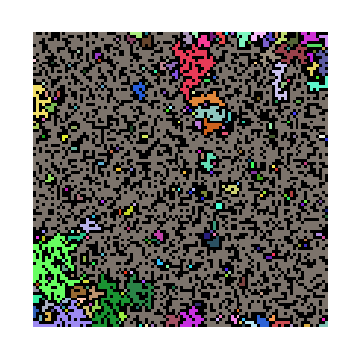

```mathematica
ArrayPlot[clusters,ImageSize->Medium,ColorRules->RandomColorRule[Union[Flatten[clusters]]]]
```

### Animation

```mathematica
Manipulate[clust=HoshenKapelman[GenerateSample[120,p]];ArrayPlot[clust,ImageSize->Large,ColorRules->RandomColorRule[Union[Flatten[clust]]]],{p,0.5,0.65,0.01}]
```

```mathematica
k=8.99*10^9;
```

```mathematica
k*(8.571*10^-11)
```

0.770533

```mathematica
k*(2.8571*10^-10)
```

2.56853